### Prepare

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/WhyMathematica/exoplanets

## Benford’s Law

### Introduction to Benford’s Law

Wikipedia:https://en.wikipedia.org/wiki/Benford’s_law

The distribution of first digits, according to Benford’s law. Each bar represents a digit, and the height of the bar is the percentage of numbers that start with that digit. (From that wikipedia page)

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/thumb/4/46/Rozklad_benforda.svg/512px-Rozklad_benforda.svg.png"]
```

-Graphics-

Here is the theoretical histogram of Benfold’s law.

```mathematica
benList=Table[N@Log10[1+1/d],{d,1,9}];
```

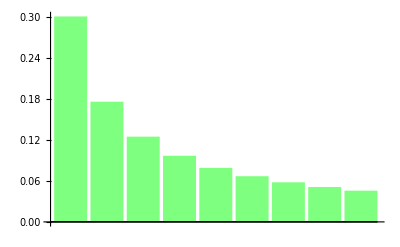

```mathematica
barBen=BarChart[Style[benList,Green],ChartBaseStyle->Opacity[0.5],ChartStyle->EdgeForm[None]]
```

### Benford’s Law of Exoplents

Here we are going to test Benfold’s Law on Exoplanets.

```mathematica
name = AstronomicalData["Exoplanet"];
```

#### Mass Data

```mathematica
massRaw = AstronomicalData["Exoplanet","Mass"];
mass = Delete[massRaw,Position[massRaw,Missing["NotAvailable"]]];
lenM=Length@mass
```

545

```mathematica
sortM=Sort@Table[RealDigits[mass][[i,1,1]],{i,1,lenM}];
```

```mathematica
tallyM=Tally@sortM;
barListM=Table[N[tallyM[[i,2]]/lenM],{i,1,Length@tallyM}]
```

{0.311927,0.166972,0.150459,0.110092,0.0715596,0.0642202,0.0477064,0.0330275,0.0440367}

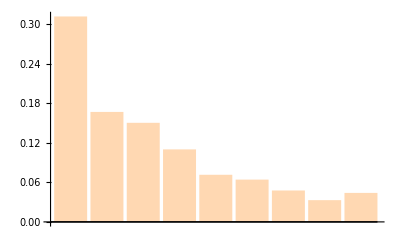

```mathematica
barM=BarChart[Style[barListM,Orange],ChartBaseStyle->Opacity[0.3],ChartStyle->EdgeForm[None]]
```

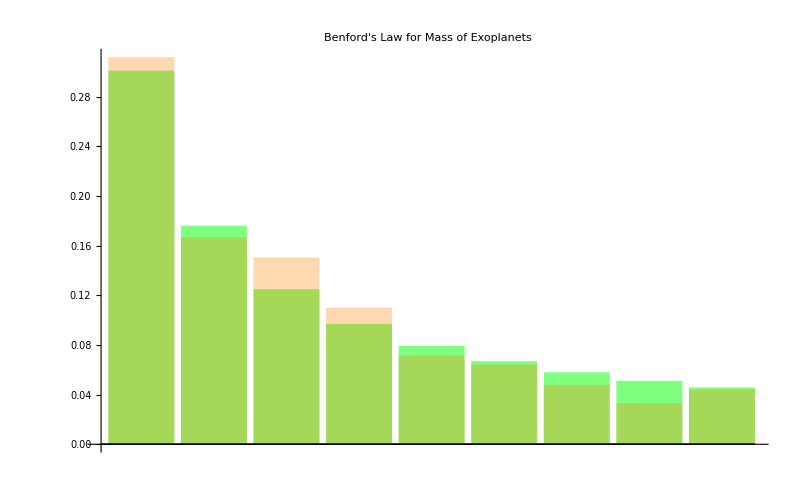

```mathematica
barMvB=Show[barBen,barM,ImageSize->800,PlotLabel->"Benford's Law for Mass of Exoplanets"]
```

```mathematica
Export["export/barMvB.png",barMvB]
```

export/barMvB.png

```mathematica
deviPerM=Table[NumberForm[(benList[[i]]-barListM[[i]])*100,3],{i,1,9}]
Grid[{Prepend[Table[i,{i,1,9}],"Number"],Prepend[deviPerM,"Deviation(%)"]},Frame->All]
```

{-1.09,0.912,-2.55,-1.32,0.762,0.273,1.03,1.81,0.172}

Number | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
Deviation(%) | -1.09 | 0.912 | -2.55 | -1.32 | 0.762 | 0.273 | 1.03 | 1.81 | 0.172

#### Radius Data

```mathematica
radiusRaw=AstronomicalData["Exoplanet","Radius"];
radius = Delete[radiusRaw,Position[radiusRaw,Missing["NotAvailable"]]];
lenR=Length@radius
```

157

```mathematica
sortR=Sort@Table[RealDigits[radius][[i,1,1]],{i,1,lenR}];
```

```mathematica
tallyR=Tally@sortR
barListR=Table[N[tallyR[[i,2]]/lenR],{i,1,Length@tallyR}]
```

{{1,35},{2,6},{3,4},{4,6},{5,6},{6,13},{7,26},{8,34},{9,27}}

{0.22293,0.0382166,0.0254777,0.0382166,0.0382166,0.0828025,0.165605,0.216561,0.171975}

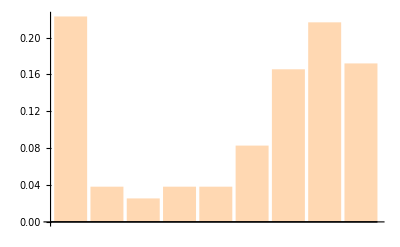

```mathematica
barR=BarChart[Style[barListR,Orange],ChartBaseStyle->Opacity[0.3],ChartStyle->EdgeForm[None]]
```

No Benfold’s Law!

### Confirmed Planet Update

data from exoplanet.eu

```mathematica
dataConM=Import["data/confirmedMass-exoplanet.eu.csv"]
```

{«1»}

```mathematica
sanConMData=Select[Table[dataConM[[i,2]]*1.89813×10^27,{i,2,Length[dataConM]}],NumberQ];
lenSanConMData=Length@sanConMData
```

1024

```mathematica
(*This step is slow!!!!*)
sortConM=Sort@Table[RealDigits[sanConMData][[i,1,1]],{i,1,lenSanConMData}];
```

```mathematica
tallyConM=Tally@sortConM
barListConM=Table[N[tallyConM[[i,2]]/lenSanConMData],{i,1,Length@tallyConM}]
```

{{1,328},{2,168},{3,149},{4,100},{5,87},{6,55},{7,60},{8,34},{9,43}}

{0.320313,0.164063,0.145508,0.0976563,0.0849609,0.0537109,0.0585938,0.0332031,0.0419922}

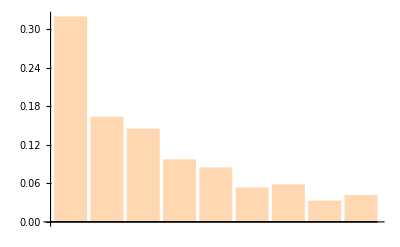

```mathematica
barConM=BarChart[Style[barListConM,Orange],ChartBaseStyle->Opacity[0.3],ChartStyle->EdgeForm[None]]
```

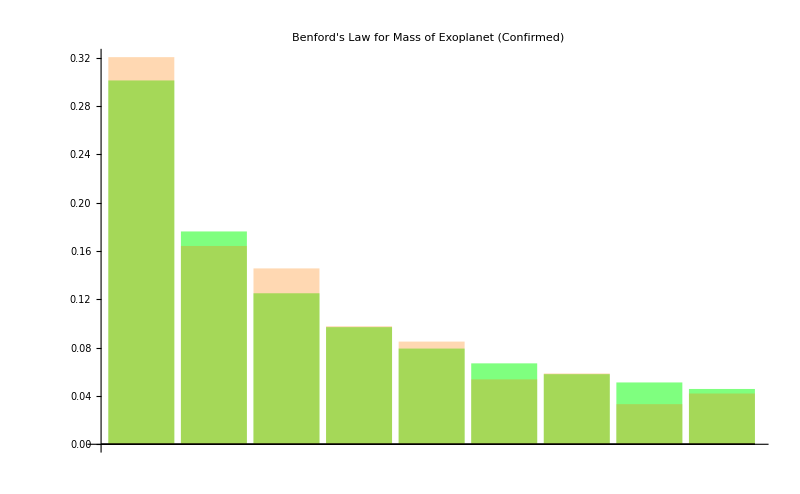

```mathematica
barConMvB=Show[barBen,barConM,ImageSize->800,PlotLabel->"Benford's Law for Mass of Exoplanet (Confirmed)"]
```

```mathematica
Export["export/barConMvB.png",barConMvB]
```

export/barConMvB.png

### All Data including KOI etc

#### Mass of Planet

From http://exoplanets.org/table

```mathematica
dataAllM=Import["data/allMass-EDE.csv"]
```

{{NAME,MASS},{,kg},{MOA-2011-BLG-293L b,5.16002×10^28},{HD 180314 b,4.29602×10^28},{CoRoT-3 b,4.14959×10^28},{HD 41004 B b,3.49617×10^28},{HD 131664 b,3.47998×10^28},{Kepler-39 b,3.45193×10^28},«5181»,{Kepler-207 b,},{KOI 5461.01,},{Kepler-181 b,},{KOI 5478.01,},{KOI 5485.01,},{Kepler-178 c,},{Kepler-83 c,},{Kepler-107 d,}}

```mathematica
Grid[dataAllM];
sanAllMData1=Select[Table[dataAllM[[i,2]],{i,2,Length[dataAllM]}],NumberQ];
sanAllMData=Delete[sanAllMData1,Position[sanAllMData,0]];
(*Got a lot of zeros in this list should drop them*)
lenSanAllMData=Length@sanAllMData
```

4261

```mathematica
(*This step is slow!!!!*)
sortAllM=Sort@Table[RealDigits[sanAllMData][[i,1,1]],{i,1,lenSanAllMData}];
```

```mathematica
sortAllMNoZero=Delete[sortAllM,Position[sortAllM,0]];
```

```mathematica
tallyAllM=Tally@sortAllMNoZero
barListAllM=Table[N[tallyAllM[[i,2]]/lenSanAllMData],{i,1,Length@tallyAllM}]
```

{{1,1257},{2,730},{3,687},{4,432},{5,297},{6,242},{7,251},{8,167},{9,168}}

{0.295001,0.171321,0.16123,0.101385,0.0697019,0.0567942,0.0589064,0.0391927,0.0394274}

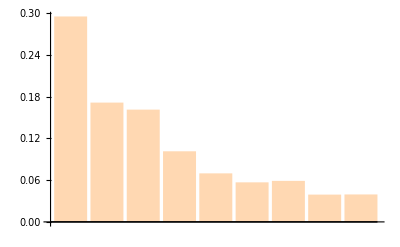

```mathematica
barAllM=BarChart[Style[barListAllM,Orange],ChartBaseStyle->Opacity[0.3],ChartStyle->EdgeForm[None]]
```

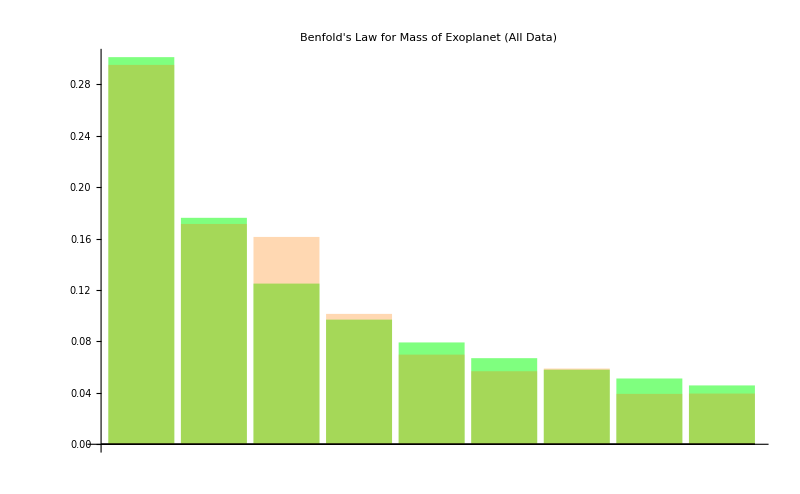

```mathematica
barAllMvB=Show[barBen,barAllM,ImageSize->800,PlotLabel->"Benford's Law for Mass of Exoplanet (All Data)"]
```

```mathematica
Export["export/barAllMvB.png",barAllMvB]
```

export/barAllMvB.png

#### Mass of Host Star

From http://exoplanets.org/table

```mathematica
dataAllMS=Import["data/allMassOfStar-EDE.csv"]
```

{{NAME,MSTAR},{,mearth},{Kepler-107 d,},{WASP-14 b,436123.},{Kepler-50 b,409489.},{NN Ser d,},{Kepler-20 b,303621.},{HAT-P-27 b,306285.},{Kepler-181 b,},«5179»,{KOI 5948.01,},{KOI 5949.01,},{KOI 5950.01,},{KOI 5952.01,},{KOI 5959.01,},{KOI 5960.01,},{KOI 5965.01,},{KOI 5968.01,},{KOI 5971.01,}}

```mathematica
Grid[dataAllMS];
sanAllMSData=Select[Table[dataAllMS[[i,2]]*5.9721986×10^24,{i,2,Length[dataAllMS]}],NumberQ];
lenSanAllMSData=Length@sanAllMSData
```

3396

```mathematica
sortAllMS=Sort@Table[RealDigits[sanAllMSData][[i,1,1]],{i,1,lenSanAllMSData}];
```

```mathematica
tallyAllMS=Tally@sortAllMS
barListAllMS=Table[N[tallyAllMS[[i,2]]/lenSanAllMSData],{i,1,Length@tallyAllMS}]
```

{{1,1873},{2,1375},{3,67},{4,29},{5,5},{6,13},{7,6},{8,5},{9,23}}

{0.551531,0.404888,0.0197291,0.00853946,0.00147232,0.00382803,0.00176678,0.00147232,0.00677267}

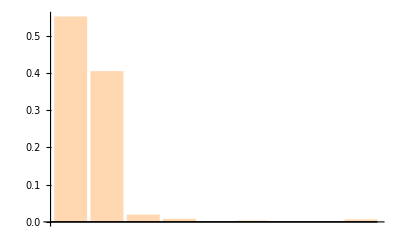

$Aborted

```mathematica
barAllMS=BarChart[Style[barListAllMS,Orange],ChartBaseStyle->Opacity[0.3],ChartStyle->EdgeForm[None]]
```